```mathematica
Clear["`*"]
```

This  Mathematica  code   produces  some  of  the  results  presented  in  Yu and Chen JMPS (2024)

#### 1 Define the basis vectors

```mathematica
eθ={1,0,0};
es={0,1,0};
nn={0,0,1};
er=es Cos[s]+nn Sin[s];
ez=es Sin[s]-nn Cos[s];
mu[Z_]=(1+Z)^2;
RR=({{1, 0, 0}, {0, Cos[s], Sin[s]}, {0, Sin[s], -Cos[s]}});(*change of coordiante matrix*)
```

#### 2 Deformation gradient F and growth tensor G, the indices (1,2,3) correspond to (θ,s,z)

```mathematica
F=({{1/(1+Z)r[s,Z]/Sin[s], 0, 0}, {0, 1/(1+Z)(Derivative[1,0][r][s,Z] Cos[s]+Derivative[1,0][z][s,Z] Sin[s]), Derivative[0,1][r][s,Z] Cos[s]+Derivative[0,1][z][s,Z] Sin[s]}, {0, 1/(1+Z)(Derivative[1,0][r][s,Z] Sin[s]-Derivative[1,0][z][s,Z] Cos[s]), Derivative[0,1][r][s,Z] Sin[s]-Derivative[0,1][z][s,Z]Cos[s]}});
F/.{r->Function[{s,Z},Sin[s]+Z Sin[s]],z->Function[{s,Z},1-Cos[s]-Z Cos[s]]}//Simplify //MatrixForm(*a simple check*)
G=({{γ1[s,Z], 0, 0}, {0, γ2[s,Z], 0}, {0, 0, 1}});(*growth tensor*)
JG=Det[G];
A=F.Inverse[G];
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### 3 Strain energy function and first P--K stress

```mathematica
CC=Transpose[A].A;
I1=Tr[CC];
J=Det[A];
W=μ/2(I1-2 Log[J])+λ/2(J-1)^2;(*compressible neo-Hookean model*)
```

#### 4 Series expansion of the energy functional

```mathematica
r[s_,Z_]=r0[s]+Z r1[s]+1/2(Z^2-1/12 H^2)r2[s];(*asymptotic solution*)
z[s_,Z_]=z0[s]+Z z1[s]+1/2(Z^2-1/12 H^2)z2[s];
γ1[s_,Z_]=γ1a[s]+γ1b [s] Z;(*Specify growth function*)
γ2[s_,Z_]=γ2a[s]+γ2b [s] Z;
Φasy=Series[JG W mu[Z],{Z,0,2}]//Normal;
Φ0=Φasy/.{Z->0};
Φ2=Coefficient[Φasy,Z^2];
Vol=Series[r[s,-H/2]^2 Derivative[1,0][z][s,-H/2],{H,0,2}]//Normal;
V=Vol-1/12 H^2 D[r0[s]^2 z2[s],s]//Simplify;
Lfull=(Φ0+1/12 H^2 Φ2)Sin[s]-1/2 P  V;(*integration of ∫ Φ μ[Z]*)
L=Series[Lfull,{H,0,2}]//Normal;
L0=L/.{H->0};
L1=Coefficient[L,H];
Lmem=L0+H L1//Simplify;
L2temp=Coefficient[L,H^2];
L2=L2temp/.{r2'[s]->0,z2'[s]->0};
L2-L2temp//Simplify
```

0

#### 5 Find the optimal r_2[s] and z_2[s]

```mathematica
DateList[]
b11=Coefficient[L2,r2[s]^2];
b12=1/2 Coefficient[L2,r2[s]z2[s]];
b22=Coefficient[L2,z2[s]^2];
L2re=L2-(b11 r2[s]^2 +2 b12 r2[s] z2[s]+b22 z2[s]^2);
c1=Coefficient[L2re,r2[s]];
c2=Coefficient[L2re,z2[s]];
L2remain=L2/.{r2[s]->0,z2[s]->0};
b11 r2[s]^2 +2 b12 r2[s] z2[s]+b22 z2[s]^2+c1 r2[s]+c2 z2[s]+L2remain-L2//Simplify
L2simp=(b22 c1^2-2 b12 c1 c2+b11 c2^2)/(4 b12^2-4 b11 b22)+L2remain//Simplify;
DateList[]
```

{2024,7,28,20,42,14.41721}

0

{2024,7,28,20,45,11.56501}

#### 6 Discrete energy

```mathematica
Lcon=Lmem+H^2 L2simp-H^2(q1[s]D[Lmem,r1[s]]+q2[s]D[Lmem,z1[s]]);
int=Lcon /.{r0[s]->𝓇0,r0'[s]->𝓇0p,z0'[s]->𝓏0p,r1[s]->𝓇1,z1[s]->𝓏1,r1'[s]->𝓇1p,z1'[s]->𝓏1p,q1[s]->𝓆1,q2[s]->𝓆2};
PK0dis=PK0/.{r0[s]->𝓇0,r0'[s]->𝓇0p,z0'[s]->𝓏0p,r1[s]->𝓇1,z1[s]->𝓏1};
```

#### 7 Shape function by linear interpolation

```mathematica
subtotal={𝓇0->N[(1-ξ)] r0[j]+N[ξ] r0[1+j],𝓇0p->1/h(-r0[j]+r0[1+j]),𝓏0p->N[(1-ξ)] z0p[j]+N[ξ] z0p[1+j],𝓇1->N[(1-ξ)] r1[j]+N[ξ]r1[1+j],𝓇1p->1/h(-r1[j]+r1[1+j]),𝓏1->N[(1-ξ)] z1[j]+N[ξ]z1[1+j],𝓏1p->1/h(-z1[j]+z1[1+j]),𝓆1->N[(1-ξ)] q1[j]+N[ξ] q1[1+j],𝓆2->N[(1-ξ)] q2[j]+N[ξ] q2[1+j],s-> j h +ξ h};
{ξ1,ξ2}={1/2(1-1/(√3)),1/2(1+1/(√3))}//N;
{ω1,ω2}={1/2,1/2}//N;
sub1=subtotal/.{ξ->ξ1};
sub2=subtotal/.{ξ->ξ2};
```

#### 8 Partition the domain and specify the growth functions

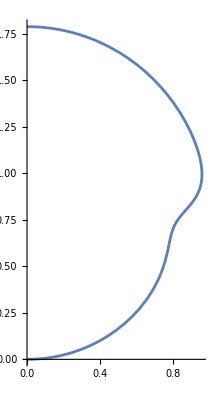

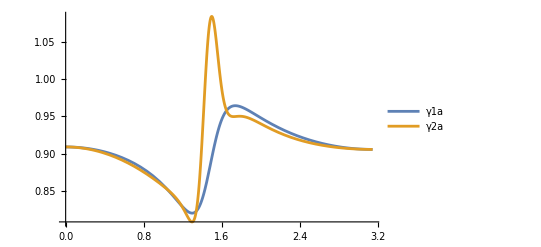

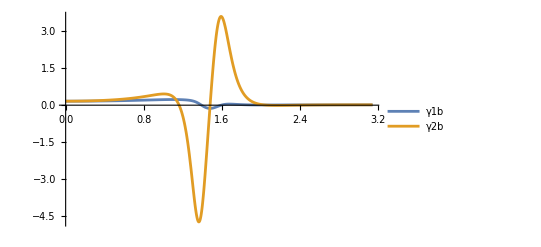

```mathematica
n=500;
h=N[π/n];
H=0.1;(*thickness of the shell*)
kr=0.9563899298924343/0.9510614820641088;
kz=1.7876604979028343/1.805503074687694;
r0ex[s_]=kr*((0.03655050592897829 (1.7170911170632295-6.410124854400475 Cos[s]+24.632408131813687 Cos[s]^2+1. Cos[s]^3) Sin[s])/(0.0674511719516303-0.22103896755925656 Cos[s]+1. Cos[s]^2));
z0ex[s_]=kz*(0.06099084887910621-0.26262889643457416 Cos[s]+1.138515532951315 Cos[s]^2-0.9003269794668691 Cos[s]^3-0.03655050592897829 Cos[s]^4)/(0.0674511719516303-0.22103896755925656 Cos[s]+1. Cos[s]^2);
γ1a[s_]=r0ex[s]/Sin[s]//Simplify;(*active stretches*)
γ2a[s_]=√(r0ex'[s]^2+z0ex'[s]^2);
γ1b[s_]=Simplify[z0ex'[s]/Sin[s]]/(√(r0ex'[s]^2+z0ex'[s]^2))-Simplify[r0ex[s]/Sin[s]];
γ2b[s_]=-(((r0ex'[s]^2+z0ex'[s]^2)^(3/2)+z0ex'[s] r0ex''[s]-r0ex'[s] z0ex''[s])/(r0ex'[s]^2+z0ex'[s]^2));
ParametricPlot[{r0ex[s],z0ex[s]},{s,0,π}]
Plot[{γ1a[s],γ2a[s]},{s,0,π},PlotRange->Full,PlotLegends->{"γ1a","γ2a"}]
Plot[{γ1b[s],γ2b[s]},{s,0,π},PlotRange->Full,PlotLegends->{"γ1b","γ2b"}]
```

#### 9 Discrete equations

```mathematica
DateList[]
ℰdis=Sum[ω1(int/.sub1)+ω2(int/.sub2),{j,0,n-1}];
eqr00=r0[0];
eqsr0=Table[D[ℰdis,r0[j]],{j,1,n-1}];
eqr0n=r0[n];
eqsz0p=Table[D[ℰdis,z0p[j]],{j,0,n}];
eqr10=r1[0];
eqsr1=Table[D[ℰdis,r1[j]],{j,1,n-1}];
eqr1n=r1[n];
eqsz1=Table[D[ℰdis,z1[j]],{j,0,n}];
eqsq1=Table[D[ℰdis,q1[j]],{j,0,n}];
eqsq2=Table[D[ℰdis,q2[j]],{j,0,n}];
eqs=Join[{eqr00==0},Table[eqsr0[[j]]==0,{j,1,Length[eqsr0]}],{eqr0n==0},Table[eqsz0p[[j]]==0,{j,1,Length[eqsz0p]}],{eqr10==0},Table[eqsr1[[j]]==0,{j,1,Length[eqsr1]}],{eqr1n==0},Table[eqsz1[[j]]==0,{j,1,Length[eqsz1]}],Table[eqsq1[[j]]==0,{j,1,Length[eqsq1]}],Table[eqsq2[[j]]==0,{j,1,Length[eqsq2]}]];
DateList[]
eqs//Length
```

{2024,7,28,20,47,8.411235}

{2024,7,28,21,4,10.04553}

3006

#### 9.1 Initial guess for q1 and q2

```mathematica
m11=(λ Csc[s] r0g[s]^2 z0g'[s]^2)/(γ1a[s] γ2a[s])+(μ Sin[s] γ1a[s] γ2a[s] (z1g[s]^2 r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2;
m12=-((Csc[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))/(γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2));
m22=(λ Csc[s] r0g[s]^2 r0g'[s]^2)/(γ1a[s] γ2a[s])+(μ Sin[s] γ1a[s] γ2a[s] ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2;
l1=-((Cos[s] (γ1a[s]^2 γ2a[s]^2 (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])-(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)))-(Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))))/(24 γ1a[s]^5 γ2a[s]^5))+(Sin[s] (-((Csc[s]^4 ((2 μ r1g[s] Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+2 λ r0g[s]^2 r1g[s] z0g'[s]^4-2 z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))^2+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4+λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])-z1g[s] (-2 μ r1g[s] Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]^2-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+6 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s]^2 z0g'[s]+2 λ r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]-2 μ r1g[s] Sin[s] γ1b[s] γ2a[s] z0g'[s]^2)+2 λ r0g[s] r1g[s] γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+r1g[s] (-2 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3+2 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (λ r1g[s] r0g'[s] z0g'[s]+λ (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+2 λ r0g[s] r1g[s] γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+z1g[s]^2 r0g'[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]-12 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+8 λ r0g[s] r1g[s]^3 γ1a[s] γ2a[s] z0g'[s]^4-3 r1g[s]^2 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))))-2 r1g[s] z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))-4 λ r0g[s]^2 r0g'[s] z0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4+λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])-z1g[s] (-2 μ r1g[s] Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]^2-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+6 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s]^2 z0g'[s]+2 λ r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]-2 μ r1g[s] Sin[s] γ1b[s] γ2a[s] z0g'[s]^2)+2 λ r0g[s] r1g[s] γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+r1g[s] (-2 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3+2 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (λ r1g[s] r0g'[s] z0g'[s]+λ (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+2 λ r0g[s] r1g[s] γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+z1g[s]^2 r0g'[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]-12 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+8 λ r0g[s] r1g[s]^3 γ1a[s] γ2a[s] z0g'[s]^4-3 r1g[s]^2 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))))-2 r1g[s] z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+(-2 λ r0g[s]^2 r0g'[s]^2 z0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (-2 z1g[s] r0g'[s] z0g'[s]+2 r1g[s] z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))^2))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)))+(Csc[s]^4 ((μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (-2 z1g[s] r0g'[s] z0g'[s]+2 r1g[s] z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+(2 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s] ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^3) ((μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))^2+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+(λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))^2))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)^2)-(6 Csc[s]^4 z0g'[s] ((μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))^2+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+(λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))^2))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^7 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))+γ1a[s]^2 γ2a[s]^2 (γ1a[s] γ2a[s] (γ1b[s] (2 γ2a[s]+γ2b[s])+γ1a[s] (γ2a[s]+2 γ2b[s])) (μ γ1a[s]^2 γ2a[s]^2 (2 r1g[s]+(2 z0g'[s])/(z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 λ Csc[s] r0g[s] z0g'[s] (γ1a[s] γ2a[s]+Csc[s] r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))-(2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (λ Csc[s]^2 r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (r1g[s] γ1a[s] γ2a[s] z0g'[s]+γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])-r0g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))+μ (-Csc[s]^2 r0g[s]^2 (-r1g[s] γ1a[s]+r0g[s] (γ1a[s]+γ1b[s])) γ2a[s]^3 z0g'[s]-r0g[s] γ1a[s]^3 (γ2a[s]+γ2b[s]) z0g'[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s])^2+Csc[s]^2 r0g[s]^2 γ1a[s] γ2a[s]^3 (-z1g[s] r0g'[s]+r1g[s] z0g'[s])-r0g[s] γ1a[s]^3 (γ2a[s]+γ2b[s]) z0g'[s] (Cos[s] r0g'[s]+Sin[s] z0g'[s])^2+r0g[s] γ1a[s]^3 γ2a[s] z0g'[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (Sin[s] r1g'[s]-Cos[s] z1g'[s])+r0g[s] γ1a[s]^3 γ2a[s] z0g'[s] (Cos[s] r0g'[s]+Sin[s] z0g'[s]) (Cos[s] r1g'[s]+Sin[s] z1g'[s])-γ1a[s]^2 γ2a[s]^2 (r1g[s] γ1a[s] γ2a[s] z0g'[s]+γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])-r0g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))-λ Csc[s]^2 r0g[s]^2 z0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))-λ Csc[s]^2 r0g[s] z0g'[s] (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+λ Csc[s]^2 (2 (r1g[s] γ1a[s] γ2a[s] z0g'[s]+γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])-r0g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))) (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))+2 (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (-r0g[s] (γ1b[s]^2 γ2a[s]^2 z0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] z0g'[s]+γ2a[s] (2 z0g'[s]-z1g'[s]))+γ1a[s]^2 (γ2b[s]^2 z0g'[s]+γ2a[s]^2 (3 z0g'[s]-2 z1g'[s])+γ2a[s] γ2b[s] (2 z0g'[s]-z1g'[s])))+r1g[s] γ1a[s] γ2a[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))+γ1a[s] γ2a[s] (-z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))+r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))-2 r0g[s] z0g'[s] (r0g[s] (z1g[s] (γ1b[s]^2 γ2a[s]^2 r0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] r0g'[s]+γ2a[s] (2 r0g'[s]-r1g'[s]))+γ1a[s]^2 (γ2b[s]^2 r0g'[s]+γ2a[s]^2 (3 r0g'[s]-2 r1g'[s])+γ2a[s] γ2b[s] (2 r0g'[s]-r1g'[s])))-r1g[s] (γ1b[s]^2 γ2a[s]^2 z0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] z0g'[s]+γ2a[s] (2 z0g'[s]-z1g'[s]))+γ1a[s]^2 (γ2b[s]^2 z0g'[s]+γ2a[s]^2 (3 z0g'[s]-2 z1g'[s])+γ2a[s] γ2b[s] (2 z0g'[s]-z1g'[s]))))+r1g[s] γ1a[s] γ2a[s] (-z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))+r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (Csc[s]^2 (2 r1g[s] γ1a[s]^2-4 r0g[s] γ1a[s] (γ1a[s]+γ1b[s])) γ2a[s]^4+(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] γ1a[s] γ2a[s] z0g'[s]+γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])-r0g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))) (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)+(2 γ1a[s]^2 γ2a[s]^2 z0g'[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))^2)/(r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^3)-(2 γ1a[s]^2 γ2a[s]^2 (-r0g[s] (γ1b[s]^2 γ2a[s]^2 z0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] z0g'[s]+γ2a[s] (2 z0g'[s]-z1g'[s]))+γ1a[s]^2 (γ2b[s]^2 z0g'[s]+γ2a[s]^2 (3 z0g'[s]-2 z1g'[s])+γ2a[s] γ2b[s] (2 z0g'[s]-z1g'[s])))+r1g[s] γ1a[s] γ2a[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))+γ1a[s] γ2a[s] (-z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))+r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-(2 γ1a[s]^2 γ2a[s]^2 z0g'[s] (r0g[s] (z1g[s] (γ1b[s]^2 γ2a[s]^2 r0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] r0g'[s]+γ2a[s] (2 r0g'[s]-r1g'[s]))+γ1a[s]^2 (γ2b[s]^2 r0g'[s]+γ2a[s]^2 (3 r0g'[s]-2 r1g'[s])+γ2a[s] γ2b[s] (2 r0g'[s]-r1g'[s])))-r1g[s] (γ1b[s]^2 γ2a[s]^2 z0g'[s]+γ1a[s] γ1b[s] γ2a[s] (γ2b[s] z0g'[s]+γ2a[s] (2 z0g'[s]-z1g'[s]))+γ1a[s]^2 (γ2b[s]^2 z0g'[s]+γ2a[s]^2 (3 z0g'[s]-2 z1g'[s])+γ2a[s] γ2b[s] (2 z0g'[s]-z1g'[s]))))+r1g[s] γ1a[s] γ2a[s] (-z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))+r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))-(2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s] (λ Csc[s]^2 r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))+μ (r0g[s] γ1a[s]^3 (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Csc[s]^2 r0g[s]^2 (-r1g[s] γ1a[s]+r0g[s] (γ1a[s]+γ1b[s])) γ2a[s]^3 (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] γ1a[s]^3 (γ2a[s]+γ2b[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])^2-r0g[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] r1g'[s]-Cos[s] z1g'[s])-r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]) (Cos[s] r1g'[s]+Sin[s] z1g'[s])-γ1a[s]^2 γ2a[s]^2 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))))/(24 γ1a[s]^5 γ2a[s]^5)+(5 Sin[s] (γ1a[s]^2 γ2a[s]^2 (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])-(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)))-(Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))) γ1a'[s])/(24 γ1a[s]^6 γ2a[s]^5)+(5 Sin[s] (γ1a[s]^2 γ2a[s]^2 (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])-(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)))-(Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))) γ2a'[s])/(24 γ1a[s]^5 γ2a[s]^6)-(Sin[s] ((4 Cot[s] Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))+2 γ1a[s] γ2a[s]^2 (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])-(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))) γ1a'[s]+2 γ1a[s]^2 γ2a[s] (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))+μ (-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])-(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))) γ2a'[s]+(6 Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^7 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))+(Csc[s]^4 (2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))))) (2 λ r0g[s] r0g'[s] (r0g'[s]^2+z0g'[s]^2)+(2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+(2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2) γ1a'[s])/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+(2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2) γ2a'[s])/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2-(2 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^3+λ r0g[s]^2 (2 r0g'[s] r0g''[s]+2 z0g'[s] z0g''[s])+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (-2 z1g[s] r0g'[s] r1g'[s] z0g'[s]+2 r1g[s] r1g'[s] z0g'[s]^2+2 z1g[s] r0g'[s]^2 z1g'[s]-2 r1g[s] r0g'[s] z0g'[s] z1g'[s]+2 (1+z1g[s]^2) r0g'[s] r0g''[s]-2 r1g[s] z1g[s] z0g'[s] r0g''[s]-2 r1g[s] z1g[s] r0g'[s] z0g''[s]+2 (1+r1g[s]^2) z0g'[s] z0g''[s]))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)^2)+γ1a[s]^2 γ2a[s]^2 ((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) r0g'[s] (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 λ Cot[s] Csc[s]^2 (2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))-(2 (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))) ((2 γ2a[s]+γ2b[s]) γ1a'[s]+γ2a[s] γ1b'[s]+γ1b[s] γ2a'[s]+γ1a[s] (2 γ2a'[s]+γ2b'[s])))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+(2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^3-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)-(2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (2 λ Cot[s] Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-2 λ Csc[s]^2 r0g[s] z1g[s] γ1a[s] γ2a[s] r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-λ Csc[s]^2 r0g[s]^2 γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) z1g'[s]-λ Csc[s]^2 r0g[s]^2 z1g[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) γ1a'[s]-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) γ2a'[s]-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s])-λ Csc[s]^2 r0g[s]^2 z1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] γ1a[s] γ2a[s]+r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])+Sin[s] γ2a[s] γ1a'[s]+Sin[s] γ1a[s] γ2a'[s]+r0g[s] (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))+μ (z1g[s] γ1a[s]^3 γ2a[s]^3 r0g'[s]-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-Sin[s] γ1a[s]^3 γ2a[s] r0g'[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])+r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])-Cos[s] γ1a[s]^3 γ2a[s] r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+r0g[s] γ1a[s]^3 γ2a[s]^3 z1g'[s]+3 r0g[s] z1g[s] γ1a[s]^2 γ2a[s]^3 γ1a'[s]-3 r0g[s] Sin[s] γ1a[s]^2 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s]) γ1a'[s]-3 Cos[s] r0g[s] γ1a[s]^2 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]) γ1a'[s]+3 r0g[s] z1g[s] γ1a[s]^3 γ2a[s]^2 γ2a'[s]-r0g[s] Sin[s] γ1a[s]^3 (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s]) γ2a'[s]-Cos[s] r0g[s] γ1a[s]^3 (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]) γ2a'[s]-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]+Sin[s] r0g''[s]-Cos[s] z0g''[s])-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (Cos[s] r0g'[s]+Sin[s] z0g'[s]) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s])-Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (-Sin[s] r0g'[s]+Cos[s] z0g'[s]+Cos[s] r0g''[s]+Sin[s] z0g''[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+λ Csc[s]^2 (-2 z1g[s] γ1a[s] γ2a[s] r0g'[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))-2 r0g[s] γ1a[s] γ2a[s] z1g'[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))))-2 r0g[s] z1g[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))) γ1a'[s]-2 r0g[s] z1g[s] γ1a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))) γ2a'[s]+2 (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])) (z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s])) r0g'[s]+z1g[s] γ1a[s]^2 γ2a[s]^2 r1g'[s]+r1g[s] γ1a[s]^2 γ2a[s]^2 z1g'[s]+r0g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s])) z1g'[s]+2 r1g[s] z1g[s] γ1a[s] γ2a[s]^2 γ1a'[s]+2 r1g[s] z1g[s] γ1a[s]^2 γ2a[s] γ2a'[s]+r0g[s] z1g[s] (-γ1b[s] γ2a[s]^2 γ1a'[s]+2 γ1a[s] (-2 γ2a[s]^2-γ2a[s] γ2b[s]) γ1a'[s]-γ1a[s] γ2a[s]^2 γ1b'[s]-2 γ1a[s] γ1b[s] γ2a[s] γ2a'[s]+γ1a[s]^2 (-4 γ2a[s] γ2a'[s]-γ2b[s] γ2a'[s]-γ2a[s] γ2b'[s])))+2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Cos[s] γ1a[s] γ2a[s]+r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])+Sin[s] γ2a[s] γ1a'[s]+Sin[s] γ1a[s] γ2a'[s]+r0g[s] (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))-2 r0g[s] z1g[s] γ1a[s] γ2a[s] (γ1a[s] γ2a[s] r1g'[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g'[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))+r1g[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s]) γ1a'[s]+r1g[s] γ1a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s]) γ2a'[s]+r1g[s] γ1a[s] γ2a[s] (r1g'[s] z0g'[s]-r0g'[s] z1g'[s]-z1g[s] r0g''[s]+r1g[s] z0g''[s])+r0g[s] ((γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s])) z1g'[s]-r1g'[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))+z1g[s] ((2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]) γ1a'[s]+γ2a[s] r0g'[s] γ1b'[s]+γ1b[s] r0g'[s] γ2a'[s]+γ1b[s] γ2a[s] r0g''[s]+γ1a[s] (2 r0g'[s] γ2a'[s]-r1g'[s] γ2a'[s]+r0g'[s] γ2b'[s]+2 γ2a[s] r0g''[s]+γ2b[s] r0g''[s]-γ2a[s] r1g''[s]))-r1g[s] ((2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]) γ1a'[s]+γ2a[s] z0g'[s] γ1b'[s]+γ1b[s] z0g'[s] γ2a'[s]+γ1b[s] γ2a[s] z0g''[s]+γ1a[s] (2 z0g'[s] γ2a'[s]-z1g'[s] γ2a'[s]+z0g'[s] γ2b'[s]+2 γ2a[s] z0g''[s]+γ2b[s] z0g''[s]-γ2a[s] z1g''[s])))))+μ (-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s])+(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) r0g'[s])/(r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s])-2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s])+(2 z1g[s] γ1a[s]^3 γ2a[s]^3 r0g'[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)-(2 γ1a[s]^3 γ2a[s]^3 z1g'[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)-16 Sin[s] γ1a[s]^3 γ2a[s] (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s]) γ1a'[s]-(4 γ1a[s] γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) γ1a'[s])/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-16 Cos[s] γ1a[s]^3 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]) γ1a'[s]+8 Sin[s] γ1a[s]^3 γ2a[s]^2 (Sin[s] r1g'[s]-Cos[s] z1g'[s]) γ1a'[s]+8 Cos[s] γ1a[s]^3 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s]) γ1a'[s]-(6 z1g[s] γ1a[s]^2 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))) γ1a'[s])/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)-4 Sin[s] γ1a[s]^4 (γ2a[s]+γ2b[s]) (Sin[s] r0g'[s]-Cos[s] z0g'[s]) γ2a'[s]-(4 γ1a[s]^2 γ2a[s] (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) γ2a'[s])/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Cos[s] γ1a[s]^4 (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]) γ2a'[s]+4 Sin[s] γ1a[s]^4 γ2a[s] (Sin[s] r1g'[s]-Cos[s] z1g'[s]) γ2a'[s]+4 Cos[s] γ1a[s]^4 γ2a[s] (Cos[s] r1g'[s]+Sin[s] z1g'[s]) γ2a'[s]-(6 z1g[s] γ1a[s]^3 γ2a[s]^2 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))) γ2a'[s])/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)-4 Sin[s] γ1a[s]^4 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (γ2a'[s]+γ2b'[s])-4 Cos[s] γ1a[s]^4 γ2a[s] (Cos[s] r0g'[s]+Sin[s] z0g'[s]) (γ2a'[s]+γ2b'[s])-(2 γ1a[s]^2 γ2a[s]^2 (z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s])) r0g'[s]+z1g[s] γ1a[s]^2 γ2a[s]^2 r1g'[s]+r1g[s] γ1a[s]^2 γ2a[s]^2 z1g'[s]+r0g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s])) z1g'[s]+2 r1g[s] z1g[s] γ1a[s] γ2a[s]^2 γ1a'[s]+2 r1g[s] z1g[s] γ1a[s]^2 γ2a[s] γ2a'[s]+r0g[s] z1g[s] (-γ1b[s] γ2a[s]^2 γ1a'[s]+2 γ1a[s] (-2 γ2a[s]^2-γ2a[s] γ2b[s]) γ1a'[s]-γ1a[s] γ2a[s]^2 γ1b'[s]-2 γ1a[s] γ1b[s] γ2a[s] γ2a'[s]+γ1a[s]^2 (-4 γ2a[s] γ2a'[s]-γ2b[s] γ2a'[s]-γ2a[s] γ2b'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))-4 Sin[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]+Sin[s] r0g''[s]-Cos[s] z0g''[s])+(2 γ1a[s]^2 γ2a[s]^2 (r1g[s] z1g[s] γ1a[s]^2 γ2a[s]^2+r0g[s] z1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)+(4 z1g[s] γ1a[s]^3 γ2a[s]^3 (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^3)-4 Cos[s] γ1a[s]^4 γ2a[s] (γ2a[s]+γ2b[s]) (-Sin[s] r0g'[s]+Cos[s] z0g'[s]+Cos[s] r0g''[s]+Sin[s] z0g''[s])+2 Sin[s] γ1a[s]^4 γ2a[s]^2 (Cos[s] r1g'[s]+Sin[s] z1g'[s]+Sin[s] r1g''[s]-Cos[s] z1g''[s])+2 Cos[s] γ1a[s]^4 γ2a[s]^2 (-Sin[s] r1g'[s]+Cos[s] z1g'[s]+Cos[s] r1g''[s]+Sin[s] z1g''[s])-(2 z1g[s] γ1a[s]^3 γ2a[s]^3 (γ1a[s] γ2a[s] r1g'[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g'[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]))-r1g[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s])))+r1g[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s]) γ1a'[s]+r1g[s] γ1a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s]) γ2a'[s]+r1g[s] γ1a[s] γ2a[s] (r1g'[s] z0g'[s]-r0g'[s] z1g'[s]-z1g[s] r0g''[s]+r1g[s] z0g''[s])+r0g[s] ((γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s])) z1g'[s]-r1g'[s] (γ1b[s] γ2a[s] z0g'[s]+γ1a[s] (2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]))+z1g[s] ((2 γ2a[s] r0g'[s]+γ2b[s] r0g'[s]-γ2a[s] r1g'[s]) γ1a'[s]+γ2a[s] r0g'[s] γ1b'[s]+γ1b[s] r0g'[s] γ2a'[s]+γ1b[s] γ2a[s] r0g''[s]+γ1a[s] (2 r0g'[s] γ2a'[s]-r1g'[s] γ2a'[s]+r0g'[s] γ2b'[s]+2 γ2a[s] r0g''[s]+γ2b[s] r0g''[s]-γ2a[s] r1g''[s]))-r1g[s] ((2 γ2a[s] z0g'[s]+γ2b[s] z0g'[s]-γ2a[s] z1g'[s]) γ1a'[s]+γ2a[s] z0g'[s] γ1b'[s]+γ1b[s] z0g'[s] γ2a'[s]+γ1b[s] γ2a[s] z0g''[s]+γ1a[s] (2 z0g'[s] γ2a'[s]-z1g'[s] γ2a'[s]+z0g'[s] γ2b'[s]+2 γ2a[s] z0g''[s]+γ2b[s] z0g''[s]-γ2a[s] z1g''[s])))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2)))-(Csc[s]^4 (2 z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) r0g''[s]+2 z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) r0g''[s]+2 r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) z0g''[s]+2 r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) z0g''[s]+2 r0g'[s] z0g'[s] (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2+2 λ r0g[s] r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 γ1a'[s]+2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] γ2a'[s]+2 λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))+2 r0g'[s] z0g'[s] (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) (2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2+2 λ r0g[s] r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 γ1a'[s]+2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] γ2a'[s]+2 λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s]))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (4 λ r0g[s] r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+2 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^2-2 λ r0g[s] r1g[s]^2 z1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3-2 λ r0g[s]^2 r1g[s] z1g[s] γ1a[s] γ2a[s] r1g'[s] z0g'[s]^3+4 λ r0g[s]^2 r1g[s] z1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2 z1g'[s]-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3 z1g'[s]+(-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]) z1g'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1a'[s]-λ r0g[s]^2 r1g[s]^2 z1g[s] γ2a[s] z0g'[s]^3 γ1a'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 γ2a'[s]-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] z0g'[s]^3 γ2a'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 r0g''[s]+4 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]-3 λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^2 z0g''[s]+z1g[s] (-2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^3 z0g'[s]-2 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-2 λ r0g[s]^2 z1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] z1g'[s]-3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 z0g'[s] γ1a'[s]-λ r0g[s]^2 z1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]-3 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] γ2a'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]-2 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g''[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]))+2 (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) (4 λ r0g[s] r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+2 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^2-2 λ r0g[s] r1g[s]^2 z1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3-2 λ r0g[s]^2 r1g[s] z1g[s] γ1a[s] γ2a[s] r1g'[s] z0g'[s]^3+4 λ r0g[s]^2 r1g[s] z1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2 z1g'[s]-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3 z1g'[s]+(-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]) z1g'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1a'[s]-λ r0g[s]^2 r1g[s]^2 z1g[s] γ2a[s] z0g'[s]^3 γ1a'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 γ2a'[s]-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] z0g'[s]^3 γ2a'[s]+2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 r0g''[s]+4 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]-3 λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^2 z0g''[s]+z1g[s] (-2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^3 z0g'[s]-2 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-2 λ r0g[s]^2 z1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] z1g'[s]-3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 z0g'[s] γ1a'[s]-λ r0g[s]^2 z1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]-3 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] γ2a'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]-2 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g''[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]))+2 (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (2 μ Cos[s] (1+r1g[s]^2) Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+2 μ r1g[s] Sin[s]^2 γ1a[s]^2 γ2a[s]^2 r1g'[s] z0g'[s]^2+2 λ r0g[s] r1g[s]^2 r0g'[s] z0g'[s]^4+2 λ r0g[s]^2 r1g[s] r1g'[s] z0g'[s]^4-2 z1g[s] r0g'[s] r1g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)+2 z1g[s] r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2) z1g'[s]-2 r1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2) z1g'[s]+2 μ (1+r1g[s]^2) Sin[s]^2 γ1a[s] γ2a[s]^2 z0g'[s]^2 γ1a'[s]+2 μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s] z0g'[s]^2 γ2a'[s]+2 z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2) r0g''[s]-2 r1g[s] z1g[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2) r0g''[s]+2 μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s] z0g''[s]+4 λ r0g[s]^2 r1g[s]^2 z0g'[s]^3 z0g''[s]-2 r1g[s] z1g[s] r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2) z0g''[s]+z1g[s]^2 r0g'[s]^2 (2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2+2 λ r0g[s] r0g'[s] z0g'[s]^2+2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 γ1a'[s]+2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] γ2a'[s]+2 λ r0g[s]^2 z0g'[s] z0g''[s])-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2+2 λ r0g[s] r0g'[s] z0g'[s]^2+2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 γ1a'[s]+2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] γ2a'[s]+2 λ r0g[s]^2 z0g'[s] z0g''[s]))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) (2 λ r0g[s] r0g'[s]^3 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)+2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2) γ1a'[s]+2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2) γ2a'[s]+2 λ r0g[s]^2 r0g'[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2 r0g''[s]+2 λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (-r1g'[s] z0g'[s]+r0g'[s] z1g'[s]+z1g[s] r0g''[s]-r1g[s] z0g''[s])+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (-2 z1g[s] r0g'[s] r1g'[s] z0g'[s]+2 r1g[s] r1g'[s] z0g'[s]^2+2 z1g[s] r0g'[s]^2 z1g'[s]-2 r1g[s] r0g'[s] z0g'[s] z1g'[s]+2 (1+z1g[s]^2) r0g'[s] r0g''[s]-2 r1g[s] z1g[s] z0g'[s] r0g''[s]-2 r1g[s] z1g[s] r0g'[s] z0g''[s]+2 r1g[s]^2 z0g'[s] z0g''[s]))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (z1g[s]^3 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))))-z1g[s] (3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))))+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))))+r1g[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))) (4 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4+r1g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)+6 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z1g'[s]+2 z1g[s] r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]) z1g'[s]-(2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2) z1g'[s]+2 λ r0g[s]^2 z1g[s]^3 γ2a[s] r0g'[s]^3 γ1a'[s]+2 λ r0g[s]^2 z1g[s]^3 γ1a[s] r0g'[s]^3 γ2a'[s]+6 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^2 r0g''[s]+z1g[s]^2 (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]) r0g''[s]+z1g[s]^2 r0g'[s] (λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2-10 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]-5 λ r0g[s]^2 γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] γ1a'[s]-5 λ r0g[s]^2 r1g[s] γ2a[s] r0g'[s] z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] γ2a'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] r0g'[s] z0g'[s] γ2a'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g''[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] z0g'[s] r0g''[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g''[s])-z1g[s] (2 λ Cos[s] r0g[s] r1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]+2 λ r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 z0g'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s] z0g'[s]-8 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2-8 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^2+4 λ r0g[s] r1g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] z0g'[s] γ1a'[s]-4 λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1a'[s]+4 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] z0g'[s] γ2a'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 γ2a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] r0g''[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 r0g''[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g''[s]-8 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s])+r1g[s] (2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ Cos[s] r0g[s] r1g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]^2+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r1g'[s] z0g'[s]^2-2 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3-2 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r1g'[s] z0g'[s]^3+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 z0g'[s] γ1a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s] γ2a[s]^2 z0g'[s]^2 γ1a'[s]-λ r0g[s]^2 r1g[s]^2 γ2a[s] z0g'[s]^3 γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] γ2a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s] z0g'[s]^2 γ2a'[s]-λ r0g[s]^2 r1g[s]^2 γ1a[s] z0g'[s]^3 γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g''[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z0g''[s]-3 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 z0g''[s]))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^4-r1g[s]^3 z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-r1g[s]^2 z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))) (4 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4+r1g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)+6 λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z1g'[s]+2 z1g[s] r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]) z1g'[s]-(2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2) z1g'[s]+2 λ r0g[s]^2 z1g[s]^3 γ2a[s] r0g'[s]^3 γ1a'[s]+2 λ r0g[s]^2 z1g[s]^3 γ1a[s] r0g'[s]^3 γ2a'[s]+6 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^2 r0g''[s]+z1g[s]^2 (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s]) r0g''[s]+z1g[s]^2 r0g'[s] (λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2-10 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]-5 λ r0g[s]^2 γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] γ1a'[s]-5 λ r0g[s]^2 r1g[s] γ2a[s] r0g'[s] z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] γ2a'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] r0g'[s] z0g'[s] γ2a'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g''[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] z0g'[s] r0g''[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g''[s])-z1g[s] (2 λ Cos[s] r0g[s] r1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]+2 λ r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 z0g'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s] z0g'[s]-8 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]^2-8 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^2+4 λ r0g[s] r1g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] z0g'[s] γ1a'[s]-4 λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1a'[s]+4 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] z0g'[s] γ2a'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 γ2a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] r0g''[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 r0g''[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g''[s]-8 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s])+r1g[s] (2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ Cos[s] r0g[s] r1g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]^2+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r1g'[s] z0g'[s]^2-2 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^3-2 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r1g'[s] z0g'[s]^3+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 z0g'[s] γ1a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s] γ2a[s]^2 z0g'[s]^2 γ1a'[s]-λ r0g[s]^2 r1g[s]^2 γ2a[s] z0g'[s]^3 γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] γ2a'[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s] z0g'[s]^2 γ2a'[s]-λ r0g[s]^2 r1g[s]^2 γ1a[s] z0g'[s]^3 γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g''[s]+2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z0g''[s]-3 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^2 z0g''[s]))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (r1g'[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+3 z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))) z1g'[s]-(3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))) z1g'[s]+2 z1g[s] r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))) z1g'[s]+2 z1g[s]^3 r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))) r0g''[s]+z1g[s]^2 (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))) r0g''[s]+z1g[s]^3 r0g'[s]^2 (2 μ Cos[s] Sin[s] γ1a[s]^2 γ1b[s] γ2a[s]^3+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-2 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^3+λ γ1a[s] r0g'[s]^2 (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))+2 μ Sin[s]^2 γ1a[s] γ1b[s] γ2a[s]^3 γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) γ1a'[s]+λ r0g[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))) γ1a'[s]+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 γ1b'[s]-λ r0g[s]^2 γ2a[s] r0g'[s]^2 γ1b'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^2 γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) γ2a'[s]-λ r0g[s]^2 γ1b[s] r0g'[s]^2 γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a'[s]+γ2b'[s])-2 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] r0g''[s]+λ r0g[s] γ1a[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))) r0g''[s]+λ r0g[s] γ1a[s] r0g'[s] (-r0g'[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))+2 γ2a[s] r0g'[s] r1g'[s]+2 r1g[s] r0g'[s] γ2a'[s]+2 r1g[s] γ2a[s] r0g''[s]-r0g[s] (2 (r0g'[s]-r1g'[s]) γ2a'[s]+r0g'[s] γ2b'[s]+γ2b[s] r0g''[s]+2 γ2a[s] (r0g''[s]-r1g''[s]))))-z1g[s] (6 λ r0g[s] r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]^2+6 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s]^2 r1g'[s] z0g'[s]^2+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Cos[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))+2 λ r0g[s] r1g[s] γ1a[s] r0g'[s] r1g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)) γ1a'[s]+λ r0g[s] r1g[s]^2 r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) γ1a'[s]+3 λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s]^2 γ1b'[s]+3 λ r0g[s]^2 r1g[s]^2 γ1b[s] r0g'[s]^2 z0g'[s]^2 γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)) γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) (2 γ2a'[s]+γ2b'[s])+6 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2 r0g''[s]+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) r0g''[s]+6 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s] z0g''[s]+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) z0g''[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (-2 r1g[s] r1g'[s] z0g'[s]^2+2 r0g'[s] r0g''[s]-2 r1g[s]^2 z0g'[s] z0g''[s])+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r0g'[s] r1g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Cos[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+μ Sin[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ1b'[s]+μ Sin[s] γ1b[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ2a'[s]+2 λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s] r0g''[s]+2 λ r1g[s] r0g'[s] z0g'[s] (2 r0g'[s] r1g'[s]+r1g[s] r0g''[s]+r0g[s] r1g''[s])+2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g''[s]+μ Sin[s] γ1b[s] γ2a[s] (-2 r1g[s] r1g'[s] z0g'[s]^2+2 r0g'[s] r0g''[s]-2 r1g[s]^2 z0g'[s] z0g''[s]))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 γ2a[s] r0g'[s] r1g'[s] z0g'[s]+r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))-6 r1g[s] r0g'[s] z0g'[s] γ2a'[s]-6 r1g[s] γ2a[s] z0g'[s] r0g''[s]-6 r1g[s] γ2a[s] r0g'[s] z0g''[s]+r0g[s] ((-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])) γ2a'[s]+3 r0g'[s] z0g'[s] γ2b'[s]+3 γ2b[s] z0g'[s] r0g''[s]+3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((6 z0g'[s]-2 z1g'[s]) r0g''[s]-4 z0g'[s] r1g''[s]-4 r1g'[s] z0g''[s]+r0g'[s] (6 z0g''[s]-2 z1g''[s])))))+z1g[s]^2 r0g'[s] (λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 r1g'[s]-6 λ r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-12 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 r1g'[s] z0g'[s]+r1g'[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] r1g'[s] γ1a'[s]-6 λ r0g[s] r1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] r1g'[s] γ2a'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r1g'[s] r0g''[s]-12 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g''[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]+r1g[s] (-4 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]-Cos[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s]^2 (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))-6 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s] γ1a'[s]-2 Sin[s] γ1a[s] γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s]) γ1a'[s]+λ r0g[s]^2 r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))) γ1a'[s]+3 λ r0g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1b'[s]-4 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) z0g'[s] γ2a'[s]+3 λ r0g[s]^2 γ1b[s] r0g'[s]^2 z0g'[s] γ2a'[s]-2 Sin[s] γ1a[s]^2 γ2a[s] (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s]) γ2a'[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] (2 γ2a'[s]+γ2b'[s])+6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]+λ r0g[s]^2 γ1a[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))) r0g''[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g''[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g''[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (2 μ Cos[s] γ1b[s] γ2a[s] z0g'[s]+2 μ Sin[s] γ2a[s] z0g'[s] γ1b'[s]+2 μ Sin[s] γ1b[s] z0g'[s] γ2a'[s]-2 λ r0g'[s] r0g''[s]+2 μ Sin[s] γ1b[s] γ2a[s] z0g''[s])+λ r0g[s]^2 γ1a[s] r0g'[s] ((-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])) γ2a'[s]+3 r0g'[s] z0g'[s] γ2b'[s]+3 γ2b[s] z0g'[s] r0g''[s]+3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((6 z0g'[s]-z1g'[s]) r0g''[s]-5 z0g'[s] r1g''[s]-5 r1g'[s] z0g''[s]+r0g'[s] (6 z0g''[s]-z1g''[s])))))+r1g[s] (2 λ r0g[s] r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^3+2 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^3+Cos[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+2 λ r0g[s] r1g[s] γ1a[s] r1g'[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+2 Sin[s] γ1a[s] γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) γ1a'[s]+λ r0g[s] r1g[s]^2 z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))) γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ1a'[s]+λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^3 γ1b'[s]+λ r0g[s]^2 r1g[s]^2 γ1b[s] r0g'[s] z0g'[s]^3 γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ2a'[s]+λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] z0g'[s]^3 r0g''[s]+3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2 z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) z0g''[s]+2 λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s] (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))) z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Cos[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ2a[s] r0g'[s] γ1b'[s]+μ Sin[s] γ1b[s] r0g'[s] γ2a'[s]+μ Sin[s] γ1b[s] γ2a[s] r0g''[s]+λ r1g[s] z0g'[s] (2 r0g'[s] r1g'[s]+r1g[s] r0g''[s]+r0g[s] r1g''[s])+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g''[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 γ2a[s] r0g'[s] r1g'[s] z0g'[s]+r0g'[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))-2 r1g[s] r0g'[s] z0g'[s] γ2a'[s]-2 r1g[s] γ2a[s] z0g'[s] r0g''[s]-2 r1g[s] γ2a[s] r0g'[s] z0g''[s]+r0g[s] ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 ((r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]+z0g'[s] r1g''[s]+r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s])))))+2 (μ (1+r1g[s]^2) Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2+λ r0g[s]^2 r1g[s]^2 z0g'[s]^4+z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)-2 r1g[s] z1g[s] r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 z0g'[s]^2)) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (r1g'[s] (λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^3+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+3 z1g[s]^2 r0g'[s]^2 (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))) z1g'[s]-(3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))) z1g'[s]+2 z1g[s] r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))) z1g'[s]+2 z1g[s]^3 r0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^3+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2+λ r0g[s] γ1a[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))) r0g''[s]+z1g[s]^2 (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+r1g[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))) r0g''[s]+z1g[s]^3 r0g'[s]^2 (2 μ Cos[s] Sin[s] γ1a[s]^2 γ1b[s] γ2a[s]^3+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])-2 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^3+λ γ1a[s] r0g'[s]^2 (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s])))+2 μ Sin[s]^2 γ1a[s] γ1b[s] γ2a[s]^3 γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) γ1a'[s]+λ r0g[s] r0g'[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))) γ1a'[s]+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^3 γ1b'[s]-λ r0g[s]^2 γ2a[s] r0g'[s]^2 γ1b'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ1b[s] γ2a[s]^2 γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) γ2a'[s]-λ r0g[s]^2 γ1b[s] r0g'[s]^2 γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a'[s]+γ2b'[s])-2 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] r0g''[s]+λ r0g[s] γ1a[s] (2 r1g[s] γ2a[s] r0g'[s]-r0g[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))) r0g''[s]+λ r0g[s] γ1a[s] r0g'[s] (-r0g'[s] (γ2b[s] r0g'[s]+2 γ2a[s] (r0g'[s]-r1g'[s]))+2 γ2a[s] r0g'[s] r1g'[s]+2 r1g[s] r0g'[s] γ2a'[s]+2 r1g[s] γ2a[s] r0g''[s]-r0g[s] (2 (r0g'[s]-r1g'[s]) γ2a'[s]+r0g'[s] γ2b'[s]+γ2b[s] r0g''[s]+2 γ2a[s] (r0g''[s]-r1g''[s]))))-z1g[s] (6 λ r0g[s] r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]^2+6 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s]^2 r1g'[s] z0g'[s]^2+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+Cos[s] γ1a[s]^2 γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2))+λ r1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))+2 λ r0g[s] r1g[s] γ1a[s] r0g'[s] r1g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s]))))+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)) γ1a'[s]+λ r0g[s] r1g[s]^2 r0g'[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) γ1a'[s]+3 λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s]^2 γ1b'[s]+3 λ r0g[s]^2 r1g[s]^2 γ1b[s] r0g'[s]^2 z0g'[s]^2 γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] (2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)) γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) (2 γ2a'[s]+γ2b'[s])+6 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2 r0g''[s]+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) r0g''[s]+6 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s] z0g''[s]+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] (-6 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))) z0g''[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) (-2 r1g[s] r1g'[s] z0g'[s]^2+2 r0g'[s] r0g''[s]-2 r1g[s]^2 z0g'[s] z0g''[s])+Sin[s] γ1a[s]^2 γ2a[s]^2 (2 λ r0g'[s] r1g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Cos[s] γ1b[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2)+μ Sin[s] γ2a[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ1b'[s]+μ Sin[s] γ1b[s] (r0g'[s]^2-r1g[s]^2 z0g'[s]^2) γ2a'[s]+2 λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s] r0g''[s]+2 λ r1g[s] r0g'[s] z0g'[s] (2 r0g'[s] r1g'[s]+r1g[s] r0g''[s]+r0g[s] r1g''[s])+2 λ r1g[s] r0g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g''[s]+μ Sin[s] γ1b[s] γ2a[s] (-2 r1g[s] r1g'[s] z0g'[s]^2+2 r0g'[s] r0g''[s]-2 r1g[s]^2 z0g'[s] z0g''[s]))+λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s] z0g'[s] (-6 γ2a[s] r0g'[s] r1g'[s] z0g'[s]+r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])))-6 r1g[s] r0g'[s] z0g'[s] γ2a'[s]-6 r1g[s] γ2a[s] z0g'[s] r0g''[s]-6 r1g[s] γ2a[s] r0g'[s] z0g''[s]+r0g[s] ((-4 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-2 z1g'[s])) γ2a'[s]+3 r0g'[s] z0g'[s] γ2b'[s]+3 γ2b[s] z0g'[s] r0g''[s]+3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((6 z0g'[s]-2 z1g'[s]) r0g''[s]-4 z0g'[s] r1g''[s]-4 r1g'[s] z0g''[s]+r0g'[s] (6 z0g''[s]-2 z1g''[s])))))+z1g[s]^2 r0g'[s] (λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 r1g'[s]-6 λ r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-12 λ r0g[s] r1g[s] γ1a[s] γ2a[s] r0g'[s]^2 r1g'[s] z0g'[s]+r1g'[s] (-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+λ r0g[s]^2 γ1a[s] r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))))+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] r1g'[s] γ1a'[s]-6 λ r0g[s] r1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] r1g'[s] γ2a'[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r1g'[s] r0g''[s]-12 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] r1g''[s]-6 λ r0g[s] r1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]+r1g[s] (-4 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s]+6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]-Cos[s] γ1a[s]^2 γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s]^2 (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])))-6 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g'[s] γ1a'[s]-2 Sin[s] γ1a[s] γ2a[s]^2 (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s]) γ1a'[s]+λ r0g[s]^2 r0g'[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))) γ1a'[s]+3 λ r0g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1b'[s]-4 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) z0g'[s] γ2a'[s]+3 λ r0g[s]^2 γ1b[s] r0g'[s]^2 z0g'[s] γ2a'[s]-2 Sin[s] γ1a[s]^2 γ2a[s] (-λ r0g'[s]^2+2 μ Sin[s] γ1b[s] γ2a[s] z0g'[s]) γ2a'[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 z0g'[s] (2 γ2a'[s]+γ2b'[s])+6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]+λ r0g[s]^2 γ1a[s] (3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s]))) r0g''[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) z0g''[s]+3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g''[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (2 μ Cos[s] γ1b[s] γ2a[s] z0g'[s]+2 μ Sin[s] γ2a[s] z0g'[s] γ1b'[s]+2 μ Sin[s] γ1b[s] z0g'[s] γ2a'[s]-2 λ r0g'[s] r0g''[s]+2 μ Sin[s] γ1b[s] γ2a[s] z0g''[s])+λ r0g[s]^2 γ1a[s] r0g'[s] ((-5 r1g'[s] z0g'[s]+r0g'[s] (6 z0g'[s]-z1g'[s])) γ2a'[s]+3 r0g'[s] z0g'[s] γ2b'[s]+3 γ2b[s] z0g'[s] r0g''[s]+3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((6 z0g'[s]-z1g'[s]) r0g''[s]-5 z0g'[s] r1g''[s]-5 r1g'[s] z0g''[s]+r0g'[s] (6 z0g''[s]-z1g''[s])))))+r1g[s] (2 λ r0g[s] r1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^3+2 λ r0g[s]^2 r1g[s] γ1b[s] γ2a[s] r0g'[s] r1g'[s] z0g'[s]^3+Cos[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s])+λ r1g[s]^2 γ1a[s] r0g'[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+2 λ r0g[s] r1g[s] γ1a[s] r1g'[s] z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))))+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+2 Sin[s] γ1a[s] γ2a[s]^2 z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) γ1a'[s]+λ r0g[s] r1g[s]^2 z0g'[s]^2 (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))) γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ1a'[s]+λ r0g[s]^2 r1g[s]^2 γ2a[s] r0g'[s] z0g'[s]^3 γ1b'[s]+λ r0g[s]^2 r1g[s]^2 γ1b[s] r0g'[s] z0g'[s]^3 γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] z0g'[s] (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ2a'[s]+λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] z0g'[s]^3 r0g''[s]+3 λ r0g[s]^2 r1g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2 z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]) z0g''[s]+2 λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s] (-2 r1g[s] γ2a[s] r0g'[s] z0g'[s]+r0g[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))) z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] (μ Cos[s] γ1b[s] γ2a[s] r0g'[s]+λ r1g'[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g'[s]+μ Sin[s] γ2a[s] r0g'[s] γ1b'[s]+μ Sin[s] γ1b[s] r0g'[s] γ2a'[s]+μ Sin[s] γ1b[s] γ2a[s] r0g''[s]+λ r1g[s] z0g'[s] (2 r0g'[s] r1g'[s]+r1g[s] r0g''[s]+r0g[s] r1g''[s])+λ r1g[s] (r1g[s] r0g'[s]+r0g[s] r1g'[s]) z0g''[s])+λ r0g[s] r1g[s]^2 γ1a[s] z0g'[s]^2 (-2 γ2a[s] r0g'[s] r1g'[s] z0g'[s]+r0g'[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))-2 r1g[s] r0g'[s] z0g'[s] γ2a'[s]-2 r1g[s] γ2a[s] z0g'[s] r0g''[s]-2 r1g[s] γ2a[s] r0g'[s] z0g''[s]+r0g[s] ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s]))))+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 ((r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]+z0g'[s] r1g''[s]+r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s])))))+2 (2 λ r0g[s]^2 r1g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 z1g[s] γ1a[s] γ2a[s] z0g'[s]^3+z1g[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]-λ r0g[s]^2 z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s])) (λ r0g[s]^2 r0g'[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2+μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+r1g[s]^2 z0g'[s]^2)) (2 λ r1g[s]^4 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^4+8 λ r0g[s] r1g[s]^3 γ1a[s] γ2a[s] r1g'[s] z0g'[s]^4-3 r1g[s]^2 r1g'[s] z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g'[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g'[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-2 r1g[s] r1g'[s] z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))+2 λ r0g[s] r1g[s]^4 γ2a[s] z0g'[s]^4 γ1a'[s]+2 λ r0g[s] r1g[s]^4 γ1a[s] z0g'[s]^4 γ2a'[s]+8 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^3 z0g''[s]-2 r1g[s]^3 z0g'[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s])))) z0g''[s]-r1g[s]^2 (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))) z0g''[s]-r1g[s]^3 z0g'[s]^2 (-2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+2 λ r0g[s] γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2-Cos[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ γ1a[s] r0g'[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s])))-3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) γ1a'[s]-2 Sin[s] γ1a[s] γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))) γ1a'[s]+λ r0g[s]^2 γ2a[s] z0g'[s]^2 γ1b'[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) γ2a'[s]+λ r0g[s]^2 γ1b[s] z0g'[s]^2 γ2a'[s]-2 Sin[s] γ1a[s]^2 γ2a[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a'[s]+γ2b'[s])+2 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s] z0g''[s]+λ r0g[s] γ1a[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))) z0g''[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s] γ1a[s] z0g'[s] (r0g'[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))+6 γ2a[s] r0g'[s] z1g'[s]+6 z1g[s] r0g'[s] γ2a'[s]+6 z1g[s] γ2a[s] r0g''[s]+r0g[s] (2 (z0g'[s]-z1g'[s]) γ2a'[s]+z0g'[s] γ2b'[s]+γ2b[s] z0g''[s]+2 γ2a[s] (z0g''[s]-z1g''[s]))))+z1g[s] (2 λ r0g[s] z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^4 z0g'[s]+2 λ r0g[s] z1g[s]^2 γ1a[s] r0g'[s]^3 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+2 λ r0g[s]^2 z1g[s] γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s] z1g'[s]+2 λ r0g[s]^2 z1g[s] γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) z1g'[s]+Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s])))+λ r0g[s]^2 z1g[s]^2 r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))) γ1a'[s]+λ r0g[s]^2 z1g[s]^2 γ2a[s] r0g'[s]^3 z0g'[s] γ1b'[s]+λ r0g[s]^2 z1g[s]^2 γ1b[s] r0g'[s]^3 z0g'[s] γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))) γ2a'[s]+3 λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s] r0g''[s]+2 λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) r0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) r0g''[s]+λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g''[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s] z0g'[s]-λ z1g[s] r0g'[s]^2 z1g'[s]-λ r0g[s] r0g'[s] z1g'[s]^2+μ Sin[s] γ2a[s] z0g'[s] γ1b'[s]+μ Sin[s] γ1b[s] z0g'[s] γ2a'[s]-λ r0g[s] z1g[s] z1g'[s] r0g''[s]+μ Sin[s] γ1b[s] γ2a[s] z0g''[s]-λ r0g[s] z1g[s] r0g'[s] z1g''[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]+z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]+z1g''[s]))))+r1g[s] (-2 λ z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4 z0g'[s]-2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ Cos[s] r0g[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+2 λ Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 z0g'[s] z1g'[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s] z1g'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]^2+2 z1g[s] r0g'[s] z1g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))))-2 λ r0g[s] z1g[s]^3 γ2a[s] r0g'[s]^3 z0g'[s] γ1a'[s]-2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2 γ1a'[s]+4 λ r0g[s] Sin[s] z1g[s] γ1a[s] γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s] γ1a'[s]-2 λ r0g[s] z1g[s]^3 γ1a[s] r0g'[s]^3 z0g'[s] γ2a'[s]-2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2 γ2a'[s]+4 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s] r0g'[s] z0g'[s] z1g'[s] γ2a'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2 ((2 γ2a[s]+γ2b[s]) γ1a'[s]+γ2a[s] γ1b'[s]+γ1b[s] γ2a'[s]+γ1a[s] (2 γ2a'[s]+γ2b'[s]))-6 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] r0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s] r0g''[s]+z1g[s]^2 (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))) r0g''[s]-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g''[s]-2 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s] z0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z1g'[s] z0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g''[s]+z1g[s]^2 r0g'[s] (2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s] γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s]^2 z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))) γ1a'[s]-3 λ r0g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1b'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) r0g'[s] γ2a'[s]-3 λ r0g[s]^2 γ1b[s] r0g'[s] z0g'[s]^2 γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 r0g'[s] (2 γ2a'[s]+γ2b'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g''[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2 r0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) r0g''[s]-6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]+λ r0g[s]^2 γ1a[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))) z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s]^2 γ1a[s] z0g'[s] ((2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])) γ2a'[s]-3 r0g'[s] z0g'[s] γ2b'[s]-3 γ2b[s] z0g'[s] r0g''[s]-3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((-6 z0g'[s]+4 z1g'[s]) r0g''[s]+2 z0g'[s] r1g''[s]+2 r1g'[s] z0g''[s]+r0g'[s] (-6 z0g''[s]+4 z1g''[s])))))-r1g[s]^2 z0g'[s] (-6 λ z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]-12 λ r0g[s] z1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] z1g'[s]+z1g'[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))-6 λ r0g[s] z1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 z0g'[s] z1g'[s] γ1a'[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] z0g'[s] z1g'[s] γ2a'[s]-12 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z1g'[s] z0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g''[s]+z1g[s] (4 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+2 Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))+6 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s] γ1a'[s]+4 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s]^2 z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))) γ1a'[s]-3 λ r0g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1b'[s]+4 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) r0g'[s] γ2a'[s]-3 λ r0g[s]^2 γ1b[s] r0g'[s] z0g'[s]^2 γ2a'[s]+4 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 r0g'[s] (2 γ2a'[s]+γ2b'[s])+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g''[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2 r0g''[s]+2 Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) r0g''[s]-6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]+λ r0g[s]^2 γ1a[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))) z0g''[s]+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s]^2 γ1a[s] z0g'[s] ((r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])) γ2a'[s]-3 r0g'[s] z0g'[s] γ2b'[s]-3 γ2b[s] z0g'[s] r0g''[s]-3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((-6 z0g'[s]+5 z1g'[s]) r0g''[s]+z0g'[s] r1g''[s]+r1g'[s] z0g''[s]+r0g'[s] (-6 z0g''[s]+5 z1g''[s]))))))+2 r0g'[s] z0g'[s] (μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2+λ r0g[s]^2 (z1g[s] r0g'[s]-r1g[s] z0g'[s])^2) (2 λ r0g[s]^2 z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3+z1g[s]^2 r0g'[s] (λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]-5 λ r0g[s]^2 r1g[s] γ1a[s] γ2a[s] r0g'[s] z0g'[s])-z1g[s] (2 λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s]-4 λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^2)+r1g[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^3 z0g'[s]+λ r0g[s] r1g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s]^2-λ r0g[s]^2 r1g[s]^2 γ1a[s] γ2a[s] z0g'[s]^3)) (2 λ r1g[s]^4 γ1a[s] γ2a[s] r0g'[s] z0g'[s]^4+8 λ r0g[s] r1g[s]^3 γ1a[s] γ2a[s] r1g'[s] z0g'[s]^4-3 r1g[s]^2 r1g'[s] z0g'[s]^2 (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))))+z1g'[s] (λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))))+r1g'[s] (-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+z1g[s]^2 r0g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))))-2 r1g[s] r1g'[s] z0g'[s] (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))))+2 λ r0g[s] r1g[s]^4 γ2a[s] z0g'[s]^4 γ1a'[s]+2 λ r0g[s] r1g[s]^4 γ1a[s] z0g'[s]^4 γ2a'[s]+8 λ r0g[s] r1g[s]^4 γ1a[s] γ2a[s] z0g'[s]^3 z0g''[s]-2 r1g[s]^3 z0g'[s] (-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s] γ1a[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s])))) z0g''[s]-r1g[s]^2 (-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+z1g[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))) z0g''[s]-r1g[s]^3 z0g'[s]^2 (-2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s])+2 λ r0g[s] γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2-Cos[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ γ1a[s] r0g'[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s])))-3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) γ1a'[s]-2 Sin[s] γ1a[s] γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s] z0g'[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))) γ1a'[s]+λ r0g[s]^2 γ2a[s] z0g'[s]^2 γ1b'[s]-2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) γ2a'[s]+λ r0g[s]^2 γ1b[s] z0g'[s]^2 γ2a'[s]-2 Sin[s] γ1a[s]^2 γ2a[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]-μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a'[s]+γ2b'[s])+2 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s] z0g''[s]+λ r0g[s] γ1a[s] (6 z1g[s] γ2a[s] r0g'[s]+r0g[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))) z0g''[s]-Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s] γ1a[s] z0g'[s] (r0g'[s] (γ2b[s] z0g'[s]+2 γ2a[s] (z0g'[s]-z1g'[s]))+6 γ2a[s] r0g'[s] z1g'[s]+6 z1g[s] r0g'[s] γ2a'[s]+6 z1g[s] γ2a[s] r0g''[s]+r0g[s] (2 (z0g'[s]-z1g'[s]) γ2a'[s]+z0g'[s] γ2b'[s]+γ2b[s] z0g''[s]+2 γ2a[s] (z0g''[s]-z1g''[s]))))+z1g[s] (2 λ r0g[s] z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^4 z0g'[s]+2 λ r0g[s] z1g[s]^2 γ1a[s] r0g'[s]^3 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])))+2 λ r0g[s]^2 z1g[s] γ1b[s] γ2a[s] r0g'[s]^3 z0g'[s] z1g'[s]+2 λ r0g[s]^2 z1g[s] γ1a[s] r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) z1g'[s]+Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s])+2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s])))+λ r0g[s]^2 z1g[s]^2 r0g'[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) γ1a'[s]+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))) γ1a'[s]+λ r0g[s]^2 z1g[s]^2 γ2a[s] r0g'[s]^3 z0g'[s] γ1b'[s]+λ r0g[s]^2 z1g[s]^2 γ1b[s] r0g'[s]^3 z0g'[s] γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s]))) γ2a'[s]+3 λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s] r0g''[s]+2 λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s] (γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s]))) r0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s] z0g'[s]-λ r0g[s] z1g[s] r0g'[s] z1g'[s]) r0g''[s]+λ r0g[s]^2 z1g[s]^2 γ1b[s] γ2a[s] r0g'[s]^3 z0g''[s]+λ r0g[s]^2 z1g[s]^2 γ1a[s] r0g'[s]^2 ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]-z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]-z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]-z1g''[s])))+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s] z0g'[s]-λ z1g[s] r0g'[s]^2 z1g'[s]-λ r0g[s] r0g'[s] z1g'[s]^2+μ Sin[s] γ2a[s] z0g'[s] γ1b'[s]+μ Sin[s] γ1b[s] z0g'[s] γ2a'[s]-λ r0g[s] z1g[s] z1g'[s] r0g''[s]+μ Sin[s] γ1b[s] γ2a[s] z0g''[s]-λ r0g[s] z1g[s] r0g'[s] z1g''[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 ((-r1g'[s] z0g'[s]+r0g'[s] (2 z0g'[s]+z1g'[s])) γ2a'[s]+r0g'[s] z0g'[s] γ2b'[s]+γ2b[s] z0g'[s] r0g''[s]+γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((2 z0g'[s]+z1g'[s]) r0g''[s]-z0g'[s] r1g''[s]-r1g'[s] z0g''[s]+r0g'[s] (2 z0g''[s]+z1g''[s]))))+r1g[s] (-2 λ z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^4 z0g'[s]-2 μ Cos[s] Sin[s] γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2+2 λ Cos[s] r0g[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]+2 λ Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s]^2 z0g'[s] z1g'[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s] z1g'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]^2+2 z1g[s] r0g'[s] z1g'[s] (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))))-2 λ r0g[s] z1g[s]^3 γ2a[s] r0g'[s]^3 z0g'[s] γ1a'[s]-2 μ Sin[s]^2 γ1a[s] γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2 γ1a'[s]+4 λ r0g[s] Sin[s] z1g[s] γ1a[s] γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s] γ1a'[s]-2 λ r0g[s] z1g[s]^3 γ1a[s] r0g'[s]^3 z0g'[s] γ2a'[s]-2 μ Sin[s]^2 γ1a[s]^2 γ2a[s] (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s]^2 γ2a'[s]+4 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s] r0g'[s] z0g'[s] z1g'[s] γ2a'[s]-μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 z0g'[s]^2 ((2 γ2a[s]+γ2b[s]) γ1a'[s]+γ2a[s] γ1b'[s]+γ1b[s] γ2a'[s]+γ1a[s] (2 γ2a'[s]+γ2b'[s]))-6 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] r0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s] r0g''[s]+z1g[s]^2 (μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))) r0g''[s]-2 λ r0g[s] z1g[s]^3 γ1a[s] γ2a[s] r0g'[s]^3 z0g''[s]-2 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) z0g'[s] z0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z1g'[s] z0g''[s]+2 λ r0g[s] Sin[s] z1g[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g''[s]+z1g[s]^2 r0g'[s] (2 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])))+3 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s] γ1a'[s]+2 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s]^2 z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))) γ1a'[s]-3 λ r0g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1b'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) r0g'[s] γ2a'[s]-3 λ r0g[s]^2 γ1b[s] r0g'[s] z0g'[s]^2 γ2a'[s]+2 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 r0g'[s] (2 γ2a'[s]+γ2b'[s])+μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g''[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2 r0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) r0g''[s]-6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]+λ r0g[s]^2 γ1a[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s]))) z0g''[s]+Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s]^2 γ1a[s] z0g'[s] ((2 r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+4 z1g'[s])) γ2a'[s]-3 r0g'[s] z0g'[s] γ2b'[s]-3 γ2b[s] z0g'[s] r0g''[s]-3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((-6 z0g'[s]+4 z1g'[s]) r0g''[s]+2 z0g'[s] r1g''[s]+2 r1g'[s] z0g''[s]+r0g'[s] (-6 z0g''[s]+4 z1g''[s])))))-r1g[s]^2 z0g'[s] (-6 λ z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^3 z0g'[s]+λ Cos[s] r0g[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g'[s]+λ Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] z0g'[s] z1g'[s]-12 λ r0g[s] z1g[s] γ1a[s] γ2a[s] r0g'[s]^2 z0g'[s] z1g'[s]+z1g'[s] (2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s]^2+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+λ r0g[s]^2 γ1a[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))))-6 λ r0g[s] z1g[s]^2 γ2a[s] r0g'[s]^2 z0g'[s] γ1a'[s]+2 λ r0g[s] Sin[s] γ1a[s] γ2a[s]^2 z0g'[s] z1g'[s] γ1a'[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] r0g'[s]^2 z0g'[s] γ2a'[s]+2 λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s] z0g'[s] z1g'[s] γ2a'[s]-12 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s] z0g'[s] r0g''[s]-6 λ r0g[s] z1g[s]^2 γ1a[s] γ2a[s] r0g'[s]^2 z0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z1g'[s] z0g''[s]+λ r0g[s] Sin[s] γ1a[s]^2 γ2a[s]^2 z0g'[s] z1g''[s]+z1g[s] (4 μ Cos[s] Sin[s] γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s]-6 λ r0g[s] γ1b[s] γ2a[s] r0g'[s]^2 z0g'[s]^2+2 Cos[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s])+2 λ r0g[s] γ1a[s] r0g'[s] z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])))+6 μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g'[s] γ1a'[s]+4 Sin[s] γ1a[s] γ2a[s]^2 r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ1a'[s]+λ r0g[s]^2 z0g'[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))) γ1a'[s]-3 λ r0g[s]^2 γ2a[s] r0g'[s] z0g'[s]^2 γ1b'[s]+4 μ Sin[s]^2 γ1a[s]^3 γ2a[s] (2 γ2a[s]+γ2b[s]) r0g'[s] γ2a'[s]-3 λ r0g[s]^2 γ1b[s] r0g'[s] z0g'[s]^2 γ2a'[s]+4 Sin[s] γ1a[s]^2 γ2a[s] r0g'[s] (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) γ2a'[s]+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 r0g'[s] (2 γ2a'[s]+γ2b'[s])+2 μ Sin[s]^2 γ1a[s]^3 γ2a[s]^2 (2 γ2a[s]+γ2b[s]) r0g''[s]-3 λ r0g[s]^2 γ1b[s] γ2a[s] z0g'[s]^2 r0g''[s]+2 Sin[s] γ1a[s]^2 γ2a[s]^2 (μ Sin[s] γ1b[s] γ2a[s]-λ z0g'[s]) r0g''[s]-6 λ r0g[s]^2 γ1b[s] γ2a[s] r0g'[s] z0g'[s] z0g''[s]+λ r0g[s]^2 γ1a[s] (-3 γ2b[s] r0g'[s] z0g'[s]+γ2a[s] (r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s]))) z0g''[s]+2 Sin[s] γ1a[s]^2 γ2a[s]^2 r0g'[s] (μ Cos[s] γ1b[s] γ2a[s]+μ Sin[s] γ2a[s] γ1b'[s]+μ Sin[s] γ1b[s] γ2a'[s]-λ z0g''[s])+λ r0g[s]^2 γ1a[s] z0g'[s] ((r1g'[s] z0g'[s]+r0g'[s] (-6 z0g'[s]+5 z1g'[s])) γ2a'[s]-3 r0g'[s] z0g'[s] γ2b'[s]-3 γ2b[s] z0g'[s] r0g''[s]-3 γ2b[s] r0g'[s] z0g''[s]+γ2a[s] ((-6 z0g'[s]+5 z1g'[s]) r0g''[s]+z0g'[s] r1g''[s]+r1g'[s] z0g''[s]+r0g'[s] (-6 z0g''[s]+5 z1g''[s]))))))))/(μ (z1g[s] r0g'[s]-r1g[s] z0g'[s])^6 (λ r0g[s]^2 (r0g'[s]^2+z0g'[s]^2)+(μ Sin[s]^2 γ1a[s]^2 γ2a[s]^2 ((1+z1g[s]^2) r0g'[s]^2-2 r1g[s] z1g[s] r0g'[s] z0g'[s]+(1+r1g[s]^2) z0g'[s]^2))/(z1g[s] r0g'[s]-r1g[s] z0g'[s])^2))))/(24 γ1a[s]^5 γ2a[s]^5);
l2=-((Cos[s] (γ1a[s]^2 γ2a[s]^2 (-((2 (γ1b[s] γ2a[s]+γ1a[s] (2 γ2a[s]+γ2b[s])) (λ Csc[s]^2 r0g[s]^2 r1g[s] γ1a[s] γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+μ (-r0g[s] r1g[s] γ1a[s]^3 γ2a[s]^3+Cos[s] r0g[s] γ1a[s]^3 γ2a[s] (Sin[s] r0g'[s]-Cos[s] z0g'[s]) (z1g[s] r0g'[s]-r1g[s] z0g'[s])-r0g[s] Sin[s] γ1a[s]^3 γ2a[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]) (Cos[s] r0g'[s]+Sin[s] z0g'[s]))))/(r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s])))+λ Csc[s]^2 (2 (-r1g[s]^2 γ1a[s]^2 γ2a[s]^2-r0g[s] r1g[s] (-γ1a[s] γ1b[s] γ2a[s]^2+γ1a[s]^2 (-2 γ2a[s]^2-γ2a[s] γ2b[s]))) (Sin[s] γ1a[s] γ2a[s]+r0g[s] (z1g[s] r0g'[s]-r1g[s] z0g'[s]))+2 r0g[s] r1g[s] γ1a[s] γ2a[s] (r1g[s] γ1a[s] γ2a[s] (-z1g[s] r0g'[s]+r1g[s] z0g'[s])+r0g[s] (z1g[s] (γ1b[s] γ2a[s] r0g'[s]+γ1a[s] (2 γ2a[s] r0g'[s]+γ2b[s] r0g'[
```

#### 10. Initial guesses

```mathematica
DateList[]
μ=N[1];
ν=0.4;
λ=N[(2 ν)/(1-2 ν)];
P=N[0];
r0g[s_]=r0ex[s]; (*intial guess*)
z0g[s_]=z0ex[s];
z0pg[s_]=z0ex'[s];
r1g[s_]=z0g'[s]/(√(r0g'[s]^2+z0g'[s]^2));
z1g[s_]=-r0g'[s]/(√(r0g'[s]^2+z0g'[s]^2));
q1fun[s_]=-(-l2 m12+l1 m22)/(m12^2-m11 m22);
q2fun[s_]=-(l2 m11-l1 m12)/(m12^2-m11 m22);
q1g=Interpolation[Table[{0.02+k*0.05,q1fun[0.02+k*0.05]},{k,0,62}]];
q2g=Interpolation[Table[{0.02+k*0.05,q2fun[0.02+k*0.05]},{k,0,62}]];
guess=Chop[Join[Table[{r0[j],r0g[j h]},{j,0,n}],Table[{z0p[j],z0pg[j h]},{j,0,n}],Table[{r1[j],r1g[j h]},{j,0,n}],Table[{z1[j],z1g[j h]},{j,0,n}],Table[{q1[j],q1g[j h]},{j,0,n}],Table[{q2[j],q2g[j h]},{j,0,n}]]];
DateList[]
guess//Length
guess
```

{2024,7,28,21,9,30.195188}

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00628319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0125664} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2024,7,28,21,12,7.083237}

3006

#### 11 Solve equations

```mathematica
DateList[]
sub=FindRoot[eqs,guess];
DateList[]
sub
```

{2024,7,28,21,13,2.023073}

{2024,7,28,21,34,51.342677}

#### 12 Plot graph

{2024,7,28,21,36,0.16246}

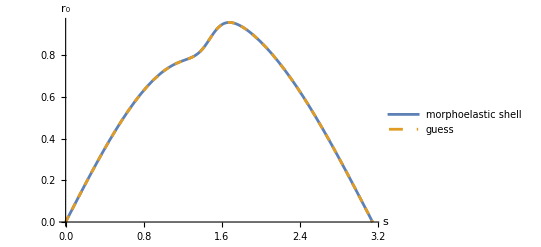

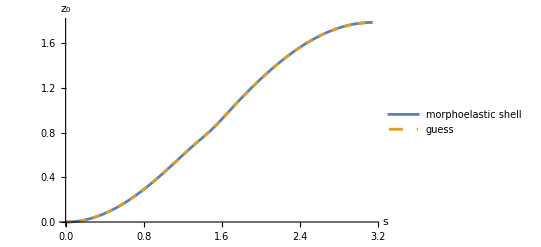

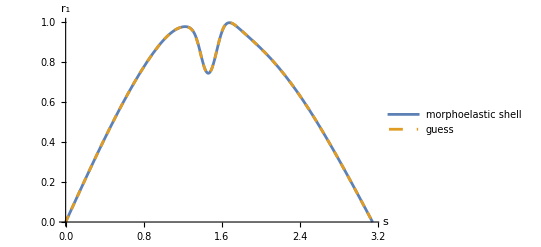

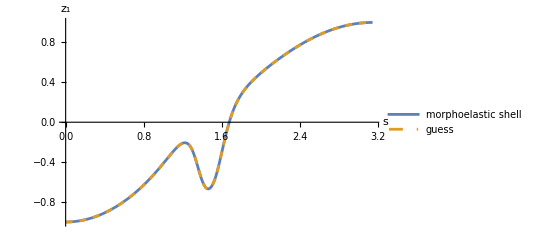

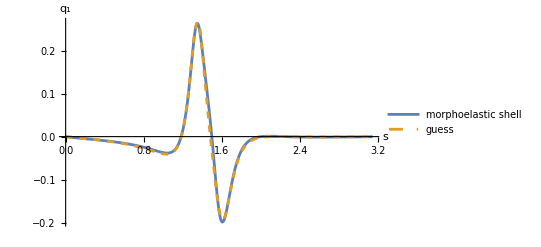

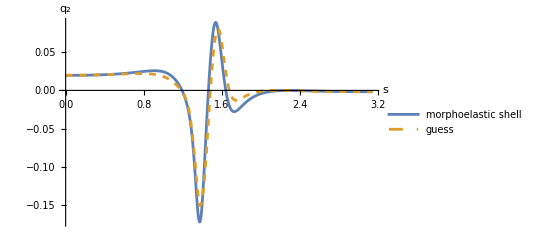

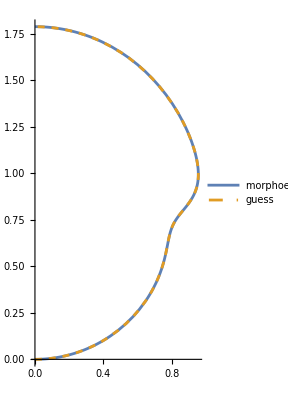

```mathematica
DateList[]
r0intp[s_]=Piecewise[Table[{((h+h j-s) r0[j]+(-h j+s) r0[1+j])/h/.sub,j h<=s<(j+1)h},{j,0,n-1}]];
z0pintp[s_]=Piecewise[Table[{((h+h j-s) z0p[j]+(-h j+s) z0p[1+j])/h/.sub,j h<=s<(j+1)h},{j,0,n-1}]];
z0[0]=0;
Table[z0[j]=Sum[h/2(z0p[i]+z0p[i+1])/.sub,{i,0,j-1}],{j,1,n}];
z0intp[s_]=Piecewise[Table[{z0[j]+(-((h j-s) ((h (2+j)-s) z0p[j]+(-h j+s) z0p[1+j]))/(2 h)/.sub),j h<=s<(j+1)h},{j,0,n-1}]];
r1intp[s_]=Piecewise[Table[{((h+h j-s) r1[j]+(-h j+s) r1[1+j])/h/.sub,j h<=s<(j+1)h},{j,0,n-1}]];
z1intp[s_]=Piecewise[Table[{((h+h j-s) z1[j]+(-h j+s) z1[1+j])/h/.sub,j h<=s<(j+1)h},{j,0,n-1}]];
Plot[{r0intp[s],r0g[s]},{s,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[r, 0]]}]
Plot[{z0intp[s],z0g[s]},{s,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[z, 0]]}]
Plot[{r1intp[s],r1g[s]},{s,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[r, 1]]}]
Plot[{z1intp[s],z1g[s]},{s,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[z, 1]]}]
ListPlot[{Table[{j h,q1[j]/.sub//Chop},{j,0,n}],Table[{j h,guess[[4n+5+j,2]]},{j,0,n}]},Joined->True,PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[q, 1]]},PlotRange->Full]
ListPlot[{Table[{j h,q2[j]/.sub//Chop},{j,0,n}],Table[{j h,guess[[5n+6+j,2]]},{j,0,n}]},Joined->True,PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[s],HoldForm[Subscript[q, 2]]},PlotRange->Full]
ParametricPlot[{{r0intp[s],z0intp[s]},{r0g[s],z0g[s]}},{s,0,π-0.001},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"}]
```

#### 13 Compare with hohn et al. BMC 2011

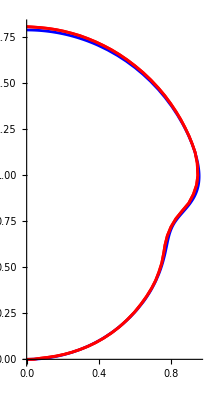

```mathematica
data={{0,1.805758},{0.00107852491929594,1.80569786718377},{0.0322108763785889,1.8038563392853},{0.075944222898086,1.8007834920455699},{0.119681167224884,1.79608011853726},{0.163422109115349,1.78956504917495},{0.207168247838581,1.78069477520246},{0.250919183638214,1.76965046620519},{0.294673317488781,1.75715680052472},{0.338434646953949,1.74140208230707},{0.382200373739151,1.72365449865004},{0.425971697113486,1.70337054079742},{0.46974821732059,1.6807313783346098},{0.513531933142294,1.65483116333463},{0.5573228445786,1.62566989579747},{0.601121351385872,1.59306640613772},{0.644927053807747,1.5572018639407998},{0.688743549651522,1.51644574293811},{0.730578772990545,1.4728350576621798},{0.766447492641499,1.4309420535379098},{0.798342354177769,1.38846702013395},{0.828252401558238,1.34474249871215},{0.85418392128894,1.3025521813105698},{0.878133191967193,1.25794987105152},{0.900095460299438,1.2130897605766},{0.918080279372304,1.1692751275975},{0.934079928315842,1.12437233380279},{0.945737883323857,1.06543725204773},{0.949066654589559,0.9980657359147401},{0.942420545090243,0.9474738653529},{0.924645698048998,0.896129173601251},{0.898913460674311,0.848004727256867},{0.863228329134774,0.806695599286706},{0.827547155183269,0.7635928924210971},{0.799821319482522,0.718199944019936},{0.780049502836524,0.671114613715042},{0.767240109577619,0.6213444263747511},{0.759983652057589,0.577132099771774},{0.748975401084592,0.521774765542742},{0.732786007781588,0.472516250361601},{0.714996429718229,0.42784765783190104},{0.69322441876612,0.38648312362931203},{0.665495468297017,0.34250178824771804},{0.633789691522206,0.29928360775801705},{0.598108627503701,0.25613107925642303},{0.556462968633778,0.213831147136211},{0.512821965834994,0.1750538201488},{0.469167771076108,0.14225508947954998},{0.425503182651687,0.114166768030671},{0.381829799587198,0.090064177460567},{0.338148021639008,0.0697661481838397},{0.29445864831985,0.0529103410296908},{0.250763678411559,0.0385909080711258},{0.207062712157766,0.026989018893544305},{0.163356549071206,0.017742334326147698},{0.119644389639145,0.0112131935397336},{0.0759294319125172,0.005952239851112399},{0.0414080201198674,0.0008429355499445009},{0.00476726259404847,0.0000830101038208006},{0,0.}};
FigH=ListPlot[{Table[{ data[[i,1]], data[[i,2]]},{i,1,Length[data]}],Table[{data[[i,1]], data[[i,2]]},{i,1,Length[data]}]},Joined->True,AspectRatio->Automatic,PlotStyle->{Red,Red}];
Figmy=ParametricPlot[{{r0intp[s],z0intp[s]}},{s,0,π-0.001},PlotStyle->{Blue,Blue}];
Show[Figmy,FigH,PlotRange->Full]
```

#### 14 Comparison with Abaqus simulation

```mathematica
datar0Abaqus={{0,-4.827648467653489*^-7},{π/100,0.0283972322901469},{π/50,0.05676147944229894},{(3 π)/100,0.08505912404152104},{π/25,0.11324183066855564},{π/20,0.14129322285648596},{(3 π)/50,0.16915778304151607},{(7 π)/100,0.19682657896577932},{(2 π)/25,0.22423325018467882},{(9 π)/100,0.2513706563770207},{π/10,0.2781966674953269},{(11 π)/100,0.30467481943047203},{(3 π)/25,0.3307807935949696},{(13 π)/100,0.3564665433838422},{(7 π)/50,0.3817237887033345},{(3 π)/20,0.40648621625174997},{(4 π)/25,0.4307697198807051},{(17 π)/100,0.4544774985307325},{(9 π)/50,0.47763928416075363},{(19 π)/100,0.5001859696349389},{π/5,0.5221031167701076},{(21 π)/100,0.5433538274204477},{(11 π)/50,0.5638863941786022},{(23 π)/100,0.5837139119444976},{(6 π)/25,0.6027097349369818},{π/4,0.6209708126206067},{(13 π)/50,0.6382760029716816},{(27 π)/100,0.654778380047158},{(7 π)/25,0.6702638181990299},{(29 π)/100,0.6848100016182441},{(3 π)/10,0.6983284868180322},{(31 π)/100,0.7107099261288862},{(8 π)/25,0.7221229959117899},{(33 π)/100,0.7321325485302803},{(17 π)/50,0.7412151517473929},{(7 π)/20,0.7488663294146939},{(9 π)/25,0.7554805816331948},{(37 π)/100,0.7609811180889189},{(19 π)/50,0.7653689495008079},{(39 π)/100,0.76928553825564},{(2 π)/5,0.7730223001296109},{(41 π)/100,0.776303967120539},{(21 π)/50,0.7837897782455592},{(43 π)/100,0.7903187610546913},{(11 π)/25,0.8072172778559547},{(9 π)/20,0.8258169669417259},{(23 π)/50,0.8482808405595111},{(47 π)/100,0.8740492163020508},{(12 π)/25,0.8981282112964661},{(49 π)/100,0.9190328169866155},{π/2,0.938926450908184},{(51 π)/100,0.9473054830236982},{(13 π)/25,0.9547742565938504},{(53 π)/100,0.9563899298924343},{(27 π)/50,0.9552351618247318},{(11 π)/20,0.9517003748325226},{(14 π)/25,0.9455300795746665},{(57 π)/100,0.9381894469599095},{(29 π)/50,0.92891291726934},{(59 π)/100,0.9187062025390971},{(3 π)/5,0.9073184826726503},{(61 π)/100,0.8949906425768813},{(31 π)/50,0.8818707502167312},{(63 π)/100,0.8679137581646025},{(16 π)/25,0.8532202036300743},{(13 π)/20,0.8378743254373952},{(33 π)/50,0.8217361616098159},{(67 π)/100,0.805127633799493},{(17 π)/25,0.787714796869708},{(69 π)/100,0.7698490400021295},{(7 π)/10,0.7512803740679788},{(71 π)/100,0.7321743483012695},{(18 π)/25,0.7125075708275947},{(73 π)/100,0.6922227406013763},{(37 π)/50,0.6715084609074917},{(3 π)/4,0.6501125851590303},{(19 π)/25,0.6284022723639303},{(77 π)/100,0.6060538520156036},{(39 π)/50,0.5833125611898632},{(79 π)/100,0.5600672715639814},{(4 π)/5,0.5363732957437823},{(81 π)/100,0.5122928092023618},{(41 π)/50,0.4877264091640915},{(83 π)/100,0.4628766386204828},{(21 π)/25,0.43755155498970055},{(17 π)/20,0.41197458586563585},{(43 π)/50,0.38600271674479264},{(87 π)/100,0.3597488333358819},{(22 π)/25,0.33320578621591457},{(89 π)/100,0.3063681799379603},{(9 π)/10,0.2793315082668828},{(91 π)/100,0.2520063715785178},{(23 π)/25,0.22455527917923906},{(93 π)/100,0.1968709359973631},{(47 π)/50,0.16905558156482292},{(19 π)/20,0.141095558021927},{(24 π)/25,0.11301358026932373},{(97 π)/100,0.08485974929871508},{(49 π)/50,0.05661243989068322},{(99 π)/100,0.02834243024305816},{π,0.0000361487218469847}};
dataz0Abaqus={{0,0.},{π/100,0.00047268874503392233},{π/50,0.001932430311967659},{(3 π)/100,0.0043456874949652224},{π/25,0.007729366000802096},{π/20,0.012069601631868654},{(3 π)/50,0.01735689169407817},{(7 π)/100,0.02360127873802842},{(2 π)/25,0.03076056975172392},{(9 π)/100,0.03887052713101169},{π/10,0.0478663286679365},{(11 π)/100,0.0577864811639347},{(3 π)/25,0.06858151833617698},{(13 π)/100,0.0802567337589174},{(7 π)/50,0.09279653452479286},{(3 π)/20,0.10616454038118872},{(4 π)/25,0.12038675015536604},{(17 π)/100,0.13538005402522701},{(9 π)/50,0.15119806484157938},{(19 π)/100,0.1677628772281129},{π/5,0.1850979235244763},{(21 π)/100,0.20316393205888672},{(11 π)/50,0.2219410128860797},{(23 π)/100,0.24142385423494206},{(6 π)/25,0.2615685463554176},{π/4,0.2823728255153868},{(13 π)/50,0.30381126848715},{(27 π)/100,0.32584964782509696},{(7 π)/25,0.3484846244536547},{(29 π)/100,0.37166502417915015},{(3 π)/10,0.3953716687803317},{(31 π)/100,0.4195765222757213},{(8 π)/25,0.44421416849094963},{(33 π)/100,0.46927802774272065},{(17 π)/50,0.4946815585366079},{(7 π)/20,0.5203314334544586},{(9 π)/25,0.5462280051451442},{(37 π)/100,0.5722193226432387},{(19 π)/50,0.5983076943569885},{(39 π)/100,0.6243118600629194},{(2 π)/5,0.6499771778693271},{(41 π)/100,0.6756794942846504},{(21 π)/50,0.7001483092607856},{(43 π)/100,0.7248447069903292},{(11 π)/25,0.7478832092174736},{(9 π)/20,0.7708210273479817},{(23 π)/50,0.7923588500318894},{(47 π)/100,0.8127134402419929},{(12 π)/25,0.8351545974068576},{(49 π)/100,0.8619206305268812},{π/2,0.8890573640455841},{(51 π)/100,0.9185789166546534},{(13 π)/25,0.9485958988594358},{(53 π)/100,0.978739361937272},{(27 π)/50,1.0089111277145255},{(11 π)/20,1.0387632619027973},{(14 π)/25,1.06822316182566},{(57 π)/100,1.0973838769098123},{(29 π)/50,1.1259570799448368},{(59 π)/100,1.1542128760267767},{(3 π)/5,1.181912491934459},{(61 π)/100,1.209196630914773},{(31 π)/50,1.2360010262297165},{(63 π)/100,1.2623074056570225},{(16 π)/25,1.2881485045491219},{(13 π)/20,1.3134676059521269},{(33 π)/50,1.3382836286533761},{(67 π)/100,1.3625877256973493},{(17 π)/25,1.3863240293224894},{(69 π)/100,1.4095666884313947},{(7 π)/10,1.4322005180900523},{(71 π)/100,1.4542931666995866},{(18 π)/25,1.4757783870446057},{(73 π)/100,1.4966519663263091},{(37 π)/50,1.5169380287125045},{(3 π)/4,1.5365241325506473},{(19 π)/25,1.555558259931561},{(77 π)/100,1.5738407818773186},{(39 π)/50,1.5915240146454128},{(79 π)/100,1.6084654405172485},{(4 π)/5,1.6247239512373612},{(81 π)/100,1.640278130888448},{(41 π)/50,1.6550558232642778},{(83 π)/100,1.6691798696104523},{(21 π)/25,1.6824405647112242},{(17 π)/20,1.6950800998032611},{(43 π)/50,1.7068443870454515},{(87 π)/100,1.7178994505454717},{(22 π)/25,1.7281365539700713},{(89 π)/100,1.7375687330350003},{(9 π)/10,1.7462527251288122},{(91 π)/100,1.7540296701205718},{(23 π)/25,1.7611388543964175},{(93 π)/100,1.7672897649437393},{(47 π)/50,1.7727511934938889},{(19 π)/20,1.7772968374985214},{(24 π)/25,1.7810562371439862},{(97 π)/100,1.7839864003368393},{(49 π)/50,1.786030310666433},{(99 π)/100,1.787338257709522},{π,1.7876604979028343}};
len=Length[datar0Abaqus];
r0Abint=Interpolation[datar0Abaqus];
z0Abint=Interpolation[dataz0Abaqus];
```

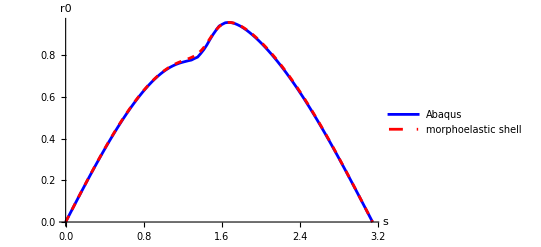

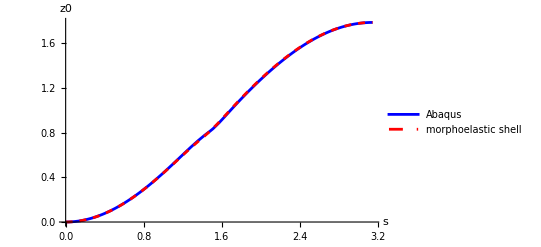

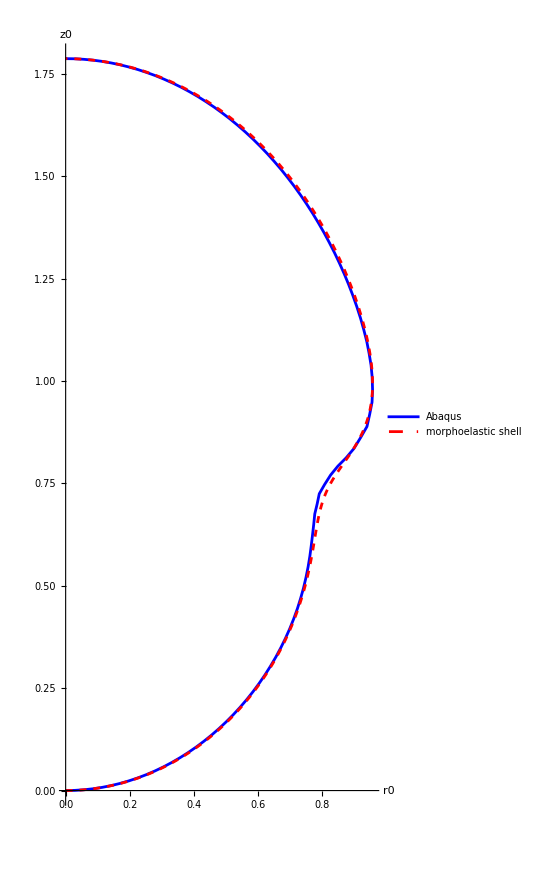

```mathematica
ListPlot[{datar0Abaqus,Table[{j h,r0[j]/.sub},{j,0,n}]},Joined->True,PlotStyle->{{Blue,Full},{Red,Dashed}},AxesLabel->{s,r0},PlotLegends->{"Abaqus","morphoelastic shell"}]
ListPlot[{dataz0Abaqus,Table[{j h,z0[j]/.sub},{j,0,n}]},Joined->True,PlotStyle->{{Blue,Full},{Red,Dashed}},AxesLabel->{s,z0},PlotLegends->{"Abaqus","morphoelastic shell"}]
ListPlot[{Table[{datar0Abaqus[[i,2]],dataz0Abaqus[[i,2]]}/.sub,{i,1,101}],Table[{r0[j],z0[j]}/.sub,{j,0,n}]},Joined->True,AspectRatio->2.2,PlotStyle->{{Blue,Full},{Red,Dashed}},AxesLabel->{r0,z0},PlotLegends->{"Abaqus","morphoelastic shell"}]
```